# Ion trap Simulation for ICL 2018 Ion trapping laboratory, QOLS group, ICL London, United Kingdom Jiyong Yu - Dept of Physics & Astronomy, Seoul National University, Republic of Korea Supervisor : Prof.Richard Thompson (02/07/2018 ~ 24/08/2018)

- Introduction -
Simulations of Penning traps in various conditions.
There are various situations and corresponding simulators.
Each simulator gives trajectory and motions of ions in Penning trap.

- Simulators -
< basics >
SingleIon[B, V0, tEnd]
SingleIonLaser[B, offset, V0, tEnd]
TwoIon[B, offset, V0, tEnd, isLaseron]
ThreeIon[B, offset, V0, tEnd, isLaseron]

< Advanced >
SingleIonAxialisation[B, offset, V0, Va, tEnd, isLaseron]
SingleIonRotatingWall[B, offset, V0, Vr, tEnd, isLaseron]

TwoIonAxialisation[B, offset, V0, Va, tEnd, isLaseron] 
TwoIonRotatingWall[B, offset, V0, Vr, tEnd, isLaseron]

ThreeIonAxialisation[B, offset, V0, Va, tEnd, isLaseron]
ThreeIonRotatingWall[B, offset, V0, Vr, tEnd, isLaseron]

## Basics of Penning trap dynamics

## - Common parameters of trap

### Basic parameters

```mathematica
SetDirectory["C:\\Users\\hp\\Desktop\\ICL\\Simulation"];
ClearAll["Global`*"];
q = 1.6*10^-19;(* charge of electon *)
u = 1.66053904×10^-27;(* atomic mass *) 
m = 40.078*u;(*mass of calcium*)
ϵ = 8.854 * 10^-12(*permittivity of vaccum*);
r0 = 10*10^-3;(*ring electrode distance from origin*)
z0 = 10*10^-3;(*endcap electrode distance from origin*)
d0 =√((r0^2+2 z0^2)/2);(*characteristic distance from origin*)
h = 6.626*10^-34;(*Plank constant*)
S0 = 1;(*Saturation parameter of laser beam*)
w = 40 * 10^-6;(*width of gaussian*)
γ = 20*10^6;(*natural linewidth*);
c = 3 * 10^8;(*speed of light*)
λ = 400 * 10^-9;(*wavelength of laser beam*)
δ = -50 * 10^6;(*detuning of laser in lab frame*)
M = 1;(*Magnification factor*)
```

## - Single Ca+ Ion dynamics

### Trap equation solving Module

```mathematica
SingleIon[B_,V0_,tEnd_]:=Module[{ωc,Vtrap,FxTrap,FyTrap,sol,xsol,ysol,result},
ωc=(q B)/m;
Vtrap[x_,y_,z_] := V0/(2 d0^2)(2 z^2-x^2-y^2);(*Potential by penning trap*)
FxTrap[x_,y_]:=-q *D[Vtrap[a,b,c],a]/.a->x/.b->y/.c->z;
FyTrap[x_,y_]:=-q *D[Vtrap[a,b,c],b]/.a->x/.b->y/.c->z;

sol = First[NDSolve[{x''[t]==ωc y'[t]+FxTrap[x[t],y[t]]/m,y''[t]==-ωc x'[t]+ FyTrap[x[t],y[t]]/m,x[0]==3.0*10^-5,y[0]==0.0*10^-5,x'[0]==0,y'[0]==10},{x[t],y[t]},{t,0,tEnd}]];(*Solution of equations of motions*)
xsol[r_]=sol[[1]][[2]]/.t->r;
ysol[r_]=sol[[2]][[2]]/.t->r;
result = Animate[Show[ParametricPlot[{x[t]/.sol,y[t]/.sol},{t,0,T},PlotStyle->{Thick,Red},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotLabel->Style["Penning trap with EM field",Bold,Italic,15]],Graphics[Disk[{xsol[T]/.sol,ysol[T]/.sol},2*10^-6],PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}}]],{T,10^-7,tEnd,10^-7},AnimationRate->40,AnimationRepetitions->Infinity];(*Trajectory and motions of ions*)
result];
```

## - Single Ca+ Ion dynamics (with laser cooling)

### Trap equation solving Module

```mathematica
SingleIonLaser[B_,offset_,V0_,tEnd_]:=Module[{ωc,Vtrap,FxTrap,FyTrap,Flaser,sol,xsol,ysol,result},
ωc=(q B)/m;
Vtrap[x_,y_,z_] := V0/(2 d0^2)(2 z^2-x^2-y^2);(*Potential by penning trap*)
FxTrap[x_,y_]:=-q *D[Vtrap[a,b,c],a]/.a->x/.b->y/.c->z;
FyTrap[x_,y_]:=-q *D[Vtrap[a,b,c],b]/.a->x/.b->y/.c->z;
Flaser[x_,y_]:=(M*h S0 Exp[-((x^2+ (y-offset)^2)/w^2)]γ)/(λ(1 + S0 Exp[-((x^2+ (y-offset)^2)/w^2)] + ((2(λ δ - D[x,t]))/(λ γ))^2));(*Force by laser cooling*)
sol = First[NDSolve[{x''[t]==ωc y'[t]+FxTrap[x[t],y[t]]/m+Flaser[x[t],y[t]]/m,y''[t]==-ωc x'[t]+ FyTrap[x[t],y[t]]/m,x[0]==3.0*10^-5,y[0]==0.0*10^-5,x'[0]==10,y'[0]==10},{x[t],y[t]},{t,0,tEnd}]];
xsol[r_]=sol[[1]][[2]]/.t->r;
ysol[r_]=sol[[2]][[2]]/.t->r;
result = Show[ParametricPlot[{xsol[t]/.sol,ysol[t]/.sol},{t,0,tEnd},PlotStyle->{Red},PlotRange->{{-7*10^-5,7*10^-5},{-7*10^-5,7*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotLabel->Style["Penning trap with Laser cooling(no Offset)",Bold,Italic,15],PlotPoints->200000]
,Graphics[Disk[{xsol[t]/.t->0,ysol[t]/.t->0},3.0*10^-6]]];(*Trajectory and motions of ions*)
result
];
```

## - Two Ca+ Ion dynamics

### Trap equation solving Module

```mathematica
TwoIon[B_,offset_,V0_,tEnd_,isLaseron_]:=Module[
{ωc,Vtrap,FxTrap,FyTrap,Fcoulomb,F1x,F1y,F2x,F2y,Flaser,sol,trajectory,motion},
ωc=(q B)/m;
Vtrap[x_,y_,z_] := V0/(2 d0^2)(2 z^2-x^2-y^2);(*Potential by penning trap*)
FxTrap[x_,y_]:=-q *D[Vtrap[a,b,c],a]/.a->x/.b->y/.c->z;
FyTrap[x_,y_]:=-q *D[Vtrap[a,b,c],b]/.a->x/.b->y/.c->z;
Fcoulomb[x1_,y1_,x2_,y2_] = q^2/(4 Pi ϵ((x2-x1)^2+(y2-y1)^2)); (*Coulomb force between two ions*)
F1x[x1_,y1_,x2_,y2_] = - Fcoulomb[x1,y1,x2,y2]*(x2-x1)/(√((x2-x1)^2 + (y2-y1)^2));
F1y[x1_,y1_,x2_,y2_] = - Fcoulomb[x1,y1,x2,y2]*(y2-y1)/(√((x2-x1)^2 + (y2-y1)^2));
F2x[x1_,y1_,x2_,y2_] = -F1x[x1,y1,x2,y2];
F2y[x1_,y1_,x2_,y2_] = -F1y[x1,y1,x2,y2];

Flaser[x_,y_]:=(M*h S0 Exp[-((x^2+ (y-offset)^2)/w^2)]γ)/(λ(1 + S0 Exp[-((x^2+ (y-offset)^2)/w^2)] + ((2(λ δ - D[x,t]))/(λ γ))^2));(*Force by laser cooling*)

sol = First[NDSolve[{x1''[t]==ωc y1'[t]+FxTrap[x1[t],y1[t]]/m +F1x[x1[t],y1[t],x2[t],y2[t]]/m+Flaser[x1[t],y1[t]]/m*isLaseron,y1''[t]==-ωc x1'[t]+ FyTrap[x1[t],y1[t]]/m + F1y[x1[t],y1[t],x2[t],y2[t]]/m,
x2''[t]==ωc y2'[t]+FxTrap[x2[t],y2[t]]/m+F2x[x1[t],y1[t],x2[t],y2[t]]/m+Flaser[x2[t],y2[t]]/m*isLaseron,
y2''[t]==-ωc x2'[t]+FyTrap[x2[t],y2[t]]/m+F2y[x1[t],y1[t],x2[t],y2[t]]/m,
x1[0]==-3.0*10^-5,y1[0]==0.0*10^-5,x1'[0]==0,y1'[0]==-5,x2[0] == 3.0 * 10^-5,y2[0] == 0.0 * 10^-5,x2'[0]==0,y2'[0] == 5},{x1[t],y1[t],x2[t],y2[t]},{t,0,tEnd},MaxSteps->Infinity]];(*solution of the equations of motion*)

trajectory = Show[ParametricPlot[{x1[t]/.sol,y1[t]/.sol},{t,0,tEnd},PlotStyle->{Thick,Red},PlotRange->{{-5*10^-5,5*10^-5},{-5*10^-5,5*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotLabel->Style["Trajectory for two ions",Bold,Italic,15],PlotPoints->2000]

,ParametricPlot[{x2[t]/.sol,y2[t]/.sol},{t,0,tEnd},PlotStyle->{Thick,Blue},PlotRange->{{-5*10^-5,5*10^-5},{-5*10^-5,5*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotPoints->2000]

  ,Graphics[Disk[{x1[t]/.sol/.t->0,y1[t]/.sol/.t->0},2.0*10^-6]]

,Graphics[Disk[{x2[t]/.sol/.t->0,y2[t]/.sol/.t->0},2.0*10^-6]]];(*trajectory of two ions*)

motion=Animate[Show[Graphics[{Red,Disk[{x1[t]/.sol/.t->T,y1[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True,AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,LabelStyle->{Bold,Black,10},
PlotLabel->Style["Motion for two ions",Bold,Italic,15]],
Graphics[{Blue,Disk[{x2[t]/.sol/.t->T,y2[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True]],
{T,0,tEnd},AnimationRate->(2*10^-8)/tEnd];(*motion of two ions*)
{trajectory,motion}
];
```

## - Three Ca+ Ion dynamics

### Trap equation solving Module

```mathematica
ThreeIon[B_,offset_,V0_,tEnd_,isLaseron_]:=Module[
{ωc,Vtrap,FxTrap,FyTrap,F12,F13,F23,F1x,F1y,F2x,F2y,F3x,F3y,Flaser,sol,trajectory,motion},

ωc=(q B)/m;
Vtrap[x_,y_,z_] := V0/(2 d0^2)(2 z^2-x^2-y^2);(*Potential by penning trap*)
FxTrap[x_,y_]:=-q *D[Vtrap[a,b,c],a]/.a->x/.b->y/.c->z;
FyTrap[x_,y_]:=-q *D[Vtrap[a,b,c],b]/.a->x/.b->y/.c->z;

F12[x1_,y1_,x2_,y2_] = q^2/(4 Pi ϵ((x2-x1)^2+(y2-y1)^2)) (*Coulomb force between 1 & 2 ions*);
F13[x1_,y1_,x3_,y3_] = q^2/(4 Pi ϵ((x3-x1)^2+(y3-y1)^2)) (*Coulomb force between 1 & 3 ions*);
F23[x2_,y2_,x3_,y3_] = q^2/(4 Pi ϵ((x3-x2)^2+(y3-y2)^2)) (*Coulomb force between 1 & 3 ions*);
F1x[x1_,y1_,x2_,y2_,x3_,y3_] = - F12[x1,y1,x2,y2]*(x2-x1)/(√((x2-x1)^2 + (y2-y1)^2)) - F13[x1,y1,x3,y3]*(x3-x1)/(√((x3-x1)^2 + (y3-y1)^2));
F1y[x1_,y1_,x2_,y2_,x3_,y3_] = - F12[x1,y1,x2,y2]*(y2-y1)/(√((x2-x1)^2 + (y2-y1)^2)) - F13[x1,y1,x3,y3]*(y3-y1)/(√((x3-x1)^2 + (y3-y1)^2));
F2x[x1_,y1_,x2_,y2_,x3_,y3_] =  F12[x1,y1,x2,y2]*(x2-x1)/(√((x2-x1)^2 + (y2-y1)^2)) - F23[x2,y2,x3,y3]*(x3-x2)/(√((x3-x2)^2 + (y3-y2)^2));
F2y[x1_,y1_,x2_,y2_,x3_,y3_] =  F12[x1,y1,x2,y2]*(y2-y1)/(√((x2-x1)^2 + (y2-y1)^2)) - F23[x2,y2,x3,y3]*(y3-y2)/(√((x3-x2)^2 + (y3-y2)^2));
F3x[x1_,y1_,x2_,y2_,x3_,y3_] =  F13[x1,y1,x3,y3]*(x3-x1)/(√((x3-x1)^2 + (y3-y1)^2)) + F23[x2,y2,x3,y3]*(x3-x2)/(√((x3-x2)^2 + (y3-y2)^2));
F3y[x1_,y1_,x2_,y2_,x3_,y3_] =  F13[x1,y1,x3,y3]*(y3-y1)/(√((x3-x1)^2 + (y3-y1)^2)) + F23[x2,y2,x3,y3]*(y3-y2)/(√((x3-x2)^2 + (y3-y2)^2));
Flaser[x_,y_]:=(M*h S0 Exp[-((x^2+ (y-offset)^2)/w^2)]γ)/(λ(1 + S0 Exp[-((x^2+ (y-offset)^2)/w^2)] + ((2(λ δ - D[x,t]))/(λ γ))^2));(*Force by laser cooling*)

sol = First[NDSolve[{x1''[t]==ωc y1'[t]+FxTrap[x1[t],y1[t]]/m+F1x[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m+Flaser[x1[t],y1[t]]/m*isLaseron,y1''[t]==-ωc x1'[t]+ FyTrap[x1[t],y1[t]]/m + F1y[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m,
x2''[t]==ωc y2'[t]+FxTrap[x2[t],y2[t]]/m+F2x[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m+Flaser[x2[t],y2[t]]/m*isLaseron,
y2''[t]==-ωc x2'[t]+FyTrap[x2[t],y2[t]]/m+F2y[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m,
x3''[t]==ωc y3'[t]+FxTrap[x3[t],y3[t]]/m+F3x[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m+Flaser[x3[t],y3[t]]/m*isLaseron,
y3''[t]==-ωc x3'[t]+FyTrap[x3[t],y3[t]]/m+F3y[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m,
x1[0]==-3.0*10^-5,y1[0]==0.0*10^-5,x1'[0]==0,y1'[0]==-5,x2[0] == 3.0 * 10^-5,y2[0] == 0.0 * 10^-5,x2'[0]==0,y2'[0] == 5
,x3[0]==0,y3[0]==3*√3*10^-5,x3'[0]==5,y3'[0]==0},{x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]},{t,0,2*tEnd},MaxSteps->Infinity]];(*numerical solution of the equations of motion*)
trajectory = Show[ParametricPlot[{x1[t]/.sol,y1[t]/.sol},{t,tEnd*0,tEnd},PlotStyle->{Thick,Red},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotLabel->Style["Trajectory for three ions",Bold,Italic,15],PlotPoints->2000]

,ParametricPlot[{x2[t]/.sol,y2[t]/.sol},{t,tEnd*0,tEnd},PlotStyle->{Thick,Blue},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotPoints->2000]

,ParametricPlot[{x3[t]/.sol,y3[t]/.sol},{t,tEnd*0,tEnd},PlotStyle->{Thick,Green},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotPoints->2000]

  ,Graphics[Disk[{x1[t]/.sol/.t->0,y1[t]/.sol/.t->0},2.0*10^-6]]

,Graphics[Disk[{x2[t]/.sol/.t->0,y2[t]/.sol/.t->0},2.0*10^-6]]
,Graphics[Disk[{x3[t]/.sol/.t->0,y3[t]/.sol/.t->0},2.0*10^-6]]];(*trajectory of three ions*)
motion = Animate[Show[Graphics[{Red,Disk[{x1[t]/.sol/.t->T,y1[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True,AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,LabelStyle->{Bold,Black,10},
PlotLabel->Style["Motion for three ions",Bold,Italic,15]],
Graphics[{Blue,Disk[{x2[t]/.sol/.t->T,y2[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True],
Graphics[{Green,Disk[{x3[t]/.sol/.t->T,y3[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True]],
{T,0,tEnd},AnimationRate->(2*10^-8)/tEnd];(*motion of three ions*)
{trajectory,motion}];
```

## Advanced methods for Penning traps

## - Axialisation

### Single Ion

```mathematica
SingleIonAxialisation[B_,offset_,V0_,Va_,tEnd_,isLaseron_]:=Module[
{ωc,Ω,Vtrap,FxTrap,FyTrap,Flaser,Vaxi,FxAxi,FyAxi,sol,trajectory,motion},
ωc=(q B)/m;
Ω = -ωc/2;
Vtrap[x_,y_,z_] := V0/(2 d0^2)(2 z^2-x^2-y^2);(*Potential by penning trap*)
FxTrap[x_,y_]:=-q *D[Vtrap[a,b,c],a]/.a->x/.b->y/.c->z;
FyTrap[x_,y_]:=-q *D[Vtrap[a,b,c],b]/.a->x/.b->y/.c->z;
Flaser[x_,y_]:=(M*h S0 Exp[-((x^2+ (y-offset)^2)/w^2)]γ)/(λ(1 + S0 Exp[-((x^2+ (y-offset)^2)/w^2)] + ((2(λ δ - D[x,t]))/(λ γ))^2));(*Force by laser cooling*)
Vaxi[x_,y_,t_]:=Va/r0^2*(x^2-y^2)*Cos[2Ω t];(*Axialisation potential*)
FxAxi[a_,b_,c_]:=-q*D[Vaxi[x,y,t],x]/.x->a/.y->b/.t->c;
FyAxi[a_,b_,c_]:=-q*D[Vaxi[x,y,t],y]/.x->a/.y->b/.t->c;
sol = First[NDSolve[{x''[t]==ωc y'[t]+FxTrap[x[t],y[t]]/m+Flaser[x[t],y[t]]/m*isLaseron + FxAxi[x[t],y[t],t]/m,y''[t]==-ωc x'[t]+ FyTrap[x[t],y[t]]/m + FyAxi[x[t],y[t],t]/m,x[0]==3.0*10^-5,y[0]==3.0*10^-5,x'[0]==30.0,y'[0]==-30.0},{x[t],y[t]},{t,0,tEnd},StartingStepSize->10*10^-9,Method->{"FixedStep",Method->"ExplicitRungeKutta"}]];
trajectory = Show[ParametricPlot[{x[t]/.sol,y[t]/.sol},{t,0,tEnd},PlotStyle->{Thick,Red},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotLabel->Style["Trajectory for axialisation",Bold,Italic,15],PlotPoints->2000],Graphics[Disk[{x[t]/.sol/.t->0,y[t]/.sol/.t->0},3.0*10^-6]]];

motion = Animate[Show[Graphics[{Black,Disk[{x[t]/.sol/.t->T,y[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True,AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,LabelStyle->{Bold,Black,10},
PlotLabel->Style["Motion with axialisation",Bold,Italic,15]]],{T,0,tEnd},AnimationRate->(2.0*10^-6)/tEnd];
{trajectory,motion,sol}];
```

### Two ions

```mathematica
TwoIonAxialisation[B_,offset_,V0_,Va_,tEnd_,isLaseron_]:=Module[
{ωc,Ω,Vtrap,FxTrap,FyTrap,Flaser,Vaxi,FxAxi,FyAxi,Fcoulomb,F1x,F1y,F2x,F2y,sol,trajectory,motion},
ωc=(q B)/m;
Ω = -ωc/2;
Vtrap[x_,y_,z_] := V0/(2 d0^2)(2 z^2-x^2-y^2);
FxTrap[x_,y_]:=-q *D[Vtrap[a,b,c],a]/.a->x/.b->y/.c->z;
FyTrap[x_,y_]:=-q *D[Vtrap[a,b,c],b]/.a->x/.b->y/.c->z;

Flaser[x_,y_]:=(M*h S0 Exp[-((x^2+ (y-offset)^2)/w^2)]γ)/(λ(1 + S0 Exp[-((x^2+ (y-offset)^2)/w^2)] + ((2(λ δ - D[x,t]))/(λ γ))^2));(*Force by laser cooling*)
Vaxi[x_,y_,t_]:=Va/r0^2*(x^2-y^2)*Cos[2Ω t];(*Axialisation potential*)
FxAxi[a_,b_,c_]:=-q*D[Vaxi[x,y,t],x]/.x->a/.y->b/.t->c;
FyAxi[a_,b_,c_]:=-q*D[Vaxi[x,y,t],y]/.x->a/.y->b/.t->c;
Fcoulomb[x1_,y1_,x2_,y2_] = q^2/(4 Pi ϵ((x2-x1)^2+(y2-y1)^2)); (*Coulomb force between two ions*)
F1x[x1_,y1_,x2_,y2_] = - Fcoulomb[x1,y1,x2,y2]*(x2-x1)/(√((x2-x1)^2 + (y2-y1)^2));
F1y[x1_,y1_,x2_,y2_] = - Fcoulomb[x1,y1,x2,y2]*(y2-y1)/(√((x2-x1)^2 + (y2-y1)^2));
F2x[x1_,y1_,x2_,y2_] = -F1x[x1,y1,x2,y2];
F2y[x1_,y1_,x2_,y2_] = -F1y[x1,y1,x2,y2];

sol = First[NDSolve[{x1''[t]==ωc y1'[t]+FxTrap[x1[t],y1[t]]/m +F1x[x1[t],y1[t],x2[t],y2[t]]/m+Flaser[x1[t],y1[t]]/m*isLaseron
+FxAxi[x1[t],y1[t],t]/m,
y1''[t]==-ωc x1'[t]+ FyTrap[x1[t],y1[t]]/m + F1y[x1[t],y1[t],x2[t],y2[t]]/m+FyAxi[x1[t],y1[t],t]/m ,
x2''[t]==ωc y2'[t]+FxTrap[x2[t],y2[t]]/m+F2x[x1[t],y1[t],x2[t],y2[t]]/m+Flaser[x2[t],y2[t]]/m*isLaseron
+FxAxi[x2[t],y2[t],t]/m,
y2''[t]==-ωc x2'[t]+FyTrap[x2[t],y2[t]]/m+F2y[x1[t],y1[t],x2[t],y2[t]]/m+FyAxi[x2[t],y2[t],t]/m,
x1[0]==-3.0*10^-5,y1[0]==-3.0*10^-5,x1'[0]==-30,y1'[0]==30,x2[0] == 3.0 * 10^-5,y2[0] == 3.0 * 10^-5,x2'[0]==30,y2'[0] == -30},{x1[t],y1[t],x2[t],y2[t]},{t,0,tEnd},StartingStepSize->10*10^-9,Method->{"FixedStep",Method->"ExplicitRungeKutta"}]];(*solution of the equations of motion*)

trajectory = Show[ParametricPlot[{x1[t]/.sol,y1[t]/.sol},{t,0,tEnd},PlotStyle->{Thick,Red},PlotRange->{{-5*10^-5,5*10^-5},{-5*10^-5,5*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotLabel->Style["Trajectory for two ions",Bold,Italic,15],PlotPoints->2000]

,ParametricPlot[{x2[t]/.sol,y2[t]/.sol},{t,0,tEnd},PlotStyle->{Thick,Blue},PlotRange->{{-5*10^-5,5*10^-5},{-5*10^-5,5*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotPoints->2000]

  ,Graphics[Disk[{x1[t]/.sol/.t->0,y1[t]/.sol/.t->0},2.0*10^-6]]

,Graphics[Disk[{x2[t]/.sol/.t->0,y2[t]/.sol/.t->0},2.0*10^-6]]];(*trajectory of two ions*)

motion = Animate[Show[Graphics[{Red,Disk[{x1[t]/.sol/.t->T,y1[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True,AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,LabelStyle->{Bold,Black,10},
PlotLabel->Style["Motion for two ions",Bold,Italic,15]],
Graphics[{Blue,Disk[{x2[t]/.sol/.t->T,y2[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True],
Graphics[{Black,Disk[{(x1[t]+x2[t])/2/.sol/.t->T,(y1[t]+y2[t])/2/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True]],
{T,0,tEnd},AnimationRate->(2*10^-6)/tEnd];(*motion of two ions*)
{sol,trajectory,motion}];
```

### Three Ions

```mathematica
ThreeIonAxialisation[B_,offset_,V0_,Va_,tEnd_,isLaseron_]:=Module[
{ωc,Ω,Vtrap,FxTrap,FyTrap,Flaser,Vaxi,FxAxi,FyAxi,F12,F13,F23,F1x,F1y,F2x,F2y,F3x,F3y,sol,trajectory,motion},
ωc=(q B)/m;
Ω = -ωc/2;
Vtrap[x_,y_,z_] := V0/(2 d0^2)(2 z^2-x^2-y^2);
FxTrap[x_,y_]:=-q *D[Vtrap[a,b,c],a]/.a->x/.b->y/.c->z;
FyTrap[x_,y_]:=-q *D[Vtrap[a,b,c],b]/.a->x/.b->y/.c->z;

Flaser[x_,y_]:=(M*h S0 Exp[-((x^2+ (y-offset)^2)/w^2)]γ)/(λ(1 + S0 Exp[-((x^2+ (y-offset)^2)/w^2)] + ((2(λ δ - D[x,t]))/(λ γ))^2));(*Force by laser cooling*)
Vaxi[x_,y_,t_]:=Va/r0^2*(x^2-y^2)*Cos[2Ω t];(*Axialisation potential*)
FxAxi[a_,b_,c_]:=-q*D[Vaxi[x,y,t],x]/.x->a/.y->b/.t->c;
FyAxi[a_,b_,c_]:=-q*D[Vaxi[x,y,t],y]/.x->a/.y->b/.t->c;
F12[x1_,y1_,x2_,y2_] = q^2/(4 Pi ϵ((x2-x1)^2+(y2-y1)^2)) (*Coulomb force between 1 & 2 ions*);
F13[x1_,y1_,x3_,y3_] = q^2/(4 Pi ϵ((x3-x1)^2+(y3-y1)^2)) (*Coulomb force between 1 & 3 ions*);
F23[x2_,y2_,x3_,y3_] = q^2/(4 Pi ϵ((x3-x2)^2+(y3-y2)^2)) (*Coulomb force between 1 & 3 ions*);
F1x[x1_,y1_,x2_,y2_,x3_,y3_] = - F12[x1,y1,x2,y2]*(x2-x1)/(√((x2-x1)^2 + (y2-y1)^2)) - F13[x1,y1,x3,y3]*(x3-x1)/(√((x3-x1)^2 + (y3-y1)^2));
F1y[x1_,y1_,x2_,y2_,x3_,y3_] = - F12[x1,y1,x2,y2]*(y2-y1)/(√((x2-x1)^2 + (y2-y1)^2)) - F13[x1,y1,x3,y3]*(y3-y1)/(√((x3-x1)^2 + (y3-y1)^2));
F2x[x1_,y1_,x2_,y2_,x3_,y3_] =  F12[x1,y1,x2,y2]*(x2-x1)/(√((x2-x1)^2 + (y2-y1)^2)) - F23[x2,y2,x3,y3]*(x3-x2)/(√((x3-x2)^2 + (y3-y2)^2));
F2y[x1_,y1_,x2_,y2_,x3_,y3_] =  F12[x1,y1,x2,y2]*(y2-y1)/(√((x2-x1)^2 + (y2-y1)^2)) - F23[x2,y2,x3,y3]*(y3-y2)/(√((x3-x2)^2 + (y3-y2)^2));
F3x[x1_,y1_,x2_,y2_,x3_,y3_] =  F13[x1,y1,x3,y3]*(x3-x1)/(√((x3-x1)^2 + (y3-y1)^2)) + F23[x2,y2,x3,y3]*(x3-x2)/(√((x3-x2)^2 + (y3-y2)^2));
F3y[x1_,y1_,x2_,y2_,x3_,y3_] =  F13[x1,y1,x3,y3]*(y3-y1)/(√((x3-x1)^2 + (y3-y1)^2)) + F23[x2,y2,x3,y3]*(y3-y2)/(√((x3-x2)^2 + (y3-y2)^2));

sol = First[NDSolve[{x1''[t]==ωc y1'[t]+FxTrap[x1[t],y1[t]]/m+F1x[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m+Flaser[x1[t],y1[t]]/m*isLaseron+FxAxi[x1[t],y1[t],t]/m,y1''[t]==-ωc x1'[t]+ FyTrap[x1[t],y1[t]]/m + F1y[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m
+FyAxi[x1[t],y1[t],t]/m,
x2''[t]==ωc y2'[t]+FxTrap[x2[t],y2[t]]/m+F2x[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m+Flaser[x2[t],y2[t]]/m*isLaseron+FxAxi[x2[t],y2[t],t]/m,
y2''[t]==-ωc x2'[t]+FyTrap[x2[t],y2[t]]/m+F2y[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m
+FyAxi[x2[t],y2[t],t]/m,
x3''[t]==ωc y3'[t]+FxTrap[x3[t],y3[t]]/m+F3x[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m+Flaser[x3[t],y3[t]]/m*isLaseron+FxAxi[x3[t],y3[t],t]/m,
y3''[t]==-ωc x3'[t]+FyTrap[x3[t],y3[t]]/m+F3y[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m
+FyAxi[x3[t],y3[t],t]/m,
x1[0]==-2.0*√3*10^-5,y1[0]==x1[0]/(√3),x1'[0]==-25.0,y1'[0]==-√3*x1'[0],x2[0] == 0.0 * 10^-5,y2[0] == -2*y1[0],x2'[0]==-2*x1'[0],y2'[0] == 0
,x3[0]==-x1[0],y3[0]==y1[0],x3'[0]==x1'[0],y3'[0]==√3*x3'[0]},{x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]},{t,0,tEnd},StartingStepSize->10*10^-9,Method->{"FixedStep",Method->"ExplicitRungeKutta"}]];(*numerical solution of the equations of motion*)
trajectory = Show[ParametricPlot[{x1[t]/.sol,y1[t]/.sol},{t,tEnd*0,tEnd},PlotStyle->{Thick,Red},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotLabel->Style["Trajectory for three ions",Bold,Italic,15],PlotPoints->2000]

,ParametricPlot[{x2[t]/.sol,y2[t]/.sol},{t,tEnd*0,tEnd},PlotStyle->{Thick,Blue},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotPoints->2000]

,ParametricPlot[{x3[t]/.sol,y3[t]/.sol},{t,tEnd*0,tEnd},PlotStyle->{Thick,Green},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotPoints->2000]

  ,Graphics[Disk[{x1[t]/.sol/.t->0,y1[t]/.sol/.t->0},2.0*10^-6]]

,Graphics[Disk[{x2[t]/.sol/.t->0,y2[t]/.sol/.t->0},2.0*10^-6]]
,Graphics[Disk[{x3[t]/.sol/.t->0,y3[t]/.sol/.t->0},2.0*10^-6]]];(*trajectory of three ions*)
motion = Animate[Show[Graphics[{Red,Disk[{x1[t]/.sol/.t->T,y1[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True,AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,LabelStyle->{Bold,Black,10},
PlotLabel->Style["Motion for three ions",Bold,Italic,15]],
Graphics[{Blue,Disk[{x2[t]/.sol/.t->T,y2[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True],
Graphics[{Green,Disk[{x3[t]/.sol/.t->T,y3[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True],
Graphics[{Black,Disk[{(x1[t]+x2[t]+x3[t])/3/.sol/.t->T,(y1[t]+y2[t]+y3[t])/3/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True]],
{T,0,tEnd},AnimationRate->(2*10^-6)/tEnd];(*motion of three ions*)
{sol,trajectory,motion}];
```

## - Rotating wall

### Single Ion

```mathematica
SingleIonRotatingWall[B_,offset_,V0_,Vr_,tEnd_,isLaseron_]:=Module[
{ωc,Ω,Vtrap,FxTrap,FyTrap,Flaser,Vrot,FxRot,FyRot,sol,trajectory,motion},
ωc=(q B)/m;
Ω = -ωc/2;
Vtrap[x_,y_,z_] := V0/(2 d0^2)(2 z^2-x^2-y^2);(*Potential by penning trap*)
FxTrap[x_,y_]:=-q *D[Vtrap[a,b,c],a]/.a->x/.b->y/.c->z;
FyTrap[x_,y_]:=-q *D[Vtrap[a,b,c],b]/.a->x/.b->y/.c->z;
Flaser[x_,y_]:=(M*h S0 Exp[-((x^2+ (y-offset)^2)/w^2)]γ)/(λ(1 + S0 Exp[-((x^2+ (y-offset)^2)/w^2)] + ((2(λ δ - D[x,t]))/(λ γ))^2));(*Force by laser cooling*)
Vrot[x_,y_,t_]:=Vr/r0^2*((x^2-y^2)*Cos[2Ω t] + 2x y Sin[2Ω t]);(*rotating wall potential*)
FxRot[a_,b_,c_]:=-q*D[Vrot[x,y,t],x]/.x->a/.y->b/.t->c;
FyRot[a_,b_,c_]:=-q*D[Vrot[x,y,t],y]/.x->a/.y->b/.t->c;
sol = First[NDSolve[{x''[t]==ωc y'[t]+FxTrap[x[t],y[t]]/m+Flaser[x[t],y[t]]/m*isLaseron + FxRot[x[t],y[t],t]/m,y''[t]==-ωc x'[t]+ FyTrap[x[t],y[t]]/m + FyRot[x[t],y[t],t]/m,x[0]==3.0*10^-5,y[0]==3.0*10^-5,x'[0]==30.0,y'[0]==-30.0},{x[t],y[t]},{t,0,tEnd},StartingStepSize->10*10^-9,Method->{"FixedStep",Method->"ExplicitRungeKutta"}]];
trajectory = Show[ParametricPlot[{x[t]/.sol,y[t]/.sol},{t,0,tEnd},PlotStyle->{Thick,Red},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotLabel->Style["Trajectory for axialisation",Bold,Italic,15],PlotPoints->2000],Graphics[Disk[{x[t]/.sol/.t->0,y[t]/.sol/.t->0},3.0*10^-6]]];

motion = Animate[Show[Graphics[{Black,Disk[{x[t]/.sol/.t->T,y[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True,AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,LabelStyle->{Bold,Black,10},
PlotLabel->Style["Motion with axialisation",Bold,Italic,15]]],{T,0,tEnd},AnimationRate->(2.0*10^-6)/tEnd];
{trajectory,motion,sol}];
```

### Two Ions

```mathematica
TwoIonRotatingWall[B_,offset_,V0_,Vr_,tEnd_,isLaseron_]:=Module[
{ωc,Ω,Vtrap,FxTrap,FyTrap,Flaser,Vrot,FxRot,FyRot,Fcoulomb,F1x,F1y,F2x,F2y,sol,trajectory,motion},
ωc=(q B)/m;
Ω = -ωc/2;
Vtrap[x_,y_,z_] := V0/(2 d0^2)(2 z^2-x^2-y^2);
FxTrap[x_,y_]:=-q *D[Vtrap[a,b,c],a]/.a->x/.b->y/.c->z;
FyTrap[x_,y_]:=-q *D[Vtrap[a,b,c],b]/.a->x/.b->y/.c->z;

Flaser[x_,y_]:=(M*h S0 Exp[-((x^2+ (y-offset)^2)/w^2)]γ)/(λ(1 + S0 Exp[-((x^2+ (y-offset)^2)/w^2)] + ((2(λ δ - D[x,t]))/(λ γ))^2));(*Force by laser cooling*)
Vrot[x_,y_,t_]:=Vr/r0^2*((x^2-y^2)*Cos[2Ω t] + 2x y Sin[2Ω t]);(*rotating wall potential*)
FxRot[a_,b_,c_]:=-q*D[Vrot[x,y,t],x]/.x->a/.y->b/.t->c;
FyRot[a_,b_,c_]:=-q*D[Vrot[x,y,t],y]/.x->a/.y->b/.t->c;
Fcoulomb[x1_,y1_,x2_,y2_] = q^2/(4 Pi ϵ((x2-x1)^2+(y2-y1)^2)); (*Coulomb force between two ions*)
F1x[x1_,y1_,x2_,y2_] = - Fcoulomb[x1,y1,x2,y2]*(x2-x1)/(√((x2-x1)^2 + (y2-y1)^2));
F1y[x1_,y1_,x2_,y2_] = - Fcoulomb[x1,y1,x2,y2]*(y2-y1)/(√((x2-x1)^2 + (y2-y1)^2));
F2x[x1_,y1_,x2_,y2_] = -F1x[x1,y1,x2,y2];
F2y[x1_,y1_,x2_,y2_] = -F1y[x1,y1,x2,y2];

sol = First[NDSolve[{x1''[t]==ωc y1'[t]+FxTrap[x1[t],y1[t]]/m +F1x[x1[t],y1[t],x2[t],y2[t]]/m+Flaser[x1[t],y1[t]]/m*isLaseron
+FxRot[x1[t],y1[t],t]/m,
y1''[t]==-ωc x1'[t]+ FyTrap[x1[t],y1[t]]/m + F1y[x1[t],y1[t],x2[t],y2[t]]/m+FyRot[x1[t],y1[t],t]/m ,
x2''[t]==ωc y2'[t]+FxTrap[x2[t],y2[t]]/m+F2x[x1[t],y1[t],x2[t],y2[t]]/m+Flaser[x2[t],y2[t]]/m*isLaseron
+FxRot[x2[t],y2[t],t]/m,
y2''[t]==-ωc x2'[t]+FyTrap[x2[t],y2[t]]/m+F2y[x1[t],y1[t],x2[t],y2[t]]/m+FyRot[x2[t],y2[t],t]/m,
x1[0]==-3.0*10^-5,y1[0]==-3.0*10^-5,x1'[0]==-30,y1'[0]==30,x2[0] == 3.0 * 10^-5,y2[0] == 3.0 * 10^-5,x2'[0]==30,y2'[0] == -30},{x1[t],y1[t],x2[t],y2[t]},{t,0,tEnd},StartingStepSize->10*10^-9,Method->{"FixedStep",Method->"ExplicitRungeKutta"}]];(*solution of the equations of motion*)

trajectory = Show[ParametricPlot[{x1[t]/.sol,y1[t]/.sol},{t,0,tEnd},PlotStyle->{Thick,Red},PlotRange->{{-5*10^-5,5*10^-5},{-5*10^-5,5*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotLabel->Style["Trajectory for two ions",Bold,Italic,15],PlotPoints->2000]

,ParametricPlot[{x2[t]/.sol,y2[t]/.sol},{t,0,tEnd},PlotStyle->{Thick,Blue},PlotRange->{{-5*10^-5,5*10^-5},{-5*10^-5,5*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotPoints->2000]

  ,Graphics[Disk[{x1[t]/.sol/.t->0,y1[t]/.sol/.t->0},2.0*10^-6]]

,Graphics[Disk[{x2[t]/.sol/.t->0,y2[t]/.sol/.t->0},2.0*10^-6]]];(*trajectory of two ions*)
motion = Animate[Show[Graphics[{Red,Disk[{x1[t]/.sol/.t->T,y1[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True,AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,LabelStyle->{Bold,Black,10},
PlotLabel->Style["Motion for two ions",Bold,Italic,15]],
Graphics[{Blue,Disk[{x2[t]/.sol/.t->T,y2[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True]],
{T,0,tEnd},AnimationRate->(2*10^-6)/tEnd];(*motion of two ions*)
{sol,trajectory,motion}];
```

### Three Ions

```mathematica
ThreeIonRotatingWall[B_,offset_,V0_,Vr_,tEnd_,isLaseron_]:=Module[
{ωc,Ω,Vtrap,FxTrap,FyTrap,Flaser,Vrot,FxRot,FyRot,F12,F13,F23,F1x,F1y,F2x,F2y,F3x,F3y,sol,trajectory,motion},
ωc=(q B)/m;
Ω = -ωc/2;
Vtrap[x_,y_,z_] := V0/(2 d0^2)(2 z^2-x^2-y^2);
FxTrap[x_,y_]:=-q *D[Vtrap[a,b,c],a]/.a->x/.b->y/.c->z;
FyTrap[x_,y_]:=-q *D[Vtrap[a,b,c],b]/.a->x/.b->y/.c->z;

Flaser[x_,y_]:=(M*h S0 Exp[-((x^2+ (y-offset)^2)/w^2)]γ)/(λ(1 + S0 Exp[-((x^2+ (y-offset)^2)/w^2)] + ((2(λ δ - D[x,t]))/(λ γ))^2));(*Force by laser cooling*)
Vrot[x_,y_,t_]:=Vr/r0^2*((x^2-y^2)*Cos[2Ω t] + 2x y Sin[2Ω t]);(*rotating wall potential*)
FxRot[a_,b_,c_]:=-q*D[Vrot[x,y,t],x]/.x->a/.y->b/.t->c;
FyRot[a_,b_,c_]:=-q*D[Vrot[x,y,t],y]/.x->a/.y->b/.t->c;
F12[x1_,y1_,x2_,y2_] = q^2/(4 Pi ϵ((x2-x1)^2+(y2-y1)^2)) (*Coulomb force between 1 & 2 ions*);
F13[x1_,y1_,x3_,y3_] = q^2/(4 Pi ϵ((x3-x1)^2+(y3-y1)^2)) (*Coulomb force between 1 & 3 ions*);
F23[x2_,y2_,x3_,y3_] = q^2/(4 Pi ϵ((x3-x2)^2+(y3-y2)^2)) (*Coulomb force between 1 & 3 ions*);
F1x[x1_,y1_,x2_,y2_,x3_,y3_] = - F12[x1,y1,x2,y2]*(x2-x1)/(√((x2-x1)^2 + (y2-y1)^2)) - F13[x1,y1,x3,y3]*(x3-x1)/(√((x3-x1)^2 + (y3-y1)^2));
F1y[x1_,y1_,x2_,y2_,x3_,y3_] = - F12[x1,y1,x2,y2]*(y2-y1)/(√((x2-x1)^2 + (y2-y1)^2)) - F13[x1,y1,x3,y3]*(y3-y1)/(√((x3-x1)^2 + (y3-y1)^2));
F2x[x1_,y1_,x2_,y2_,x3_,y3_] =  F12[x1,y1,x2,y2]*(x2-x1)/(√((x2-x1)^2 + (y2-y1)^2)) - F23[x2,y2,x3,y3]*(x3-x2)/(√((x3-x2)^2 + (y3-y2)^2));
F2y[x1_,y1_,x2_,y2_,x3_,y3_] =  F12[x1,y1,x2,y2]*(y2-y1)/(√((x2-x1)^2 + (y2-y1)^2)) - F23[x2,y2,x3,y3]*(y3-y2)/(√((x3-x2)^2 + (y3-y2)^2));
F3x[x1_,y1_,x2_,y2_,x3_,y3_] =  F13[x1,y1,x3,y3]*(x3-x1)/(√((x3-x1)^2 + (y3-y1)^2)) + F23[x2,y2,x3,y3]*(x3-x2)/(√((x3-x2)^2 + (y3-y2)^2));
F3y[x1_,y1_,x2_,y2_,x3_,y3_] =  F13[x1,y1,x3,y3]*(y3-y1)/(√((x3-x1)^2 + (y3-y1)^2)) + F23[x2,y2,x3,y3]*(y3-y2)/(√((x3-x2)^2 + (y3-y2)^2));

sol = First[NDSolve[{x1''[t]==ωc y1'[t]+FxTrap[x1[t],y1[t]]/m+F1x[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m+Flaser[x1[t],y1[t]]/m*isLaseron+FxRot[x1[t],y1[t],t]/m,y1''[t]==-ωc x1'[t]+ FyTrap[x1[t],y1[t]]/m + F1y[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m
+FyRot[x1[t],y1[t],t]/m,
x2''[t]==ωc y2'[t]+FxTrap[x2[t],y2[t]]/m+F2x[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m+Flaser[x2[t],y2[t]]/m*isLaseron+FxRot[x2[t],y2[t],t]/m,
y2''[t]==-ωc x2'[t]+FyTrap[x2[t],y2[t]]/m+F2y[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m
+FyRot[x2[t],y2[t],t]/m,
x3''[t]==ωc y3'[t]+FxTrap[x3[t],y3[t]]/m+F3x[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m+Flaser[x3[t],y3[t]]/m*isLaseron+FxRot[x3[t],y3[t],t]/m,
y3''[t]==-ωc x3'[t]+FyTrap[x3[t],y3[t]]/m+F3y[x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]]/m
+FyRot[x3[t],y3[t],t]/m,
x1[0]==-2.0*√3*10^-5,y1[0]==x1[0]/(√3),x1'[0]==-25.0,y1'[0]==-√3*x1'[0],x2[0] == 0.0 * 10^-5,y2[0] == -2*y1[0],x2'[0]==-2*x1'[0],y2'[0] == 0
,x3[0]==-x1[0],y3[0]==y1[0],x3'[0]==x1'[0],y3'[0]==√3*x3'[0]},{x1[t],y1[t],x2[t],y2[t],x3[t],y3[t]},{t,0,tEnd},StartingStepSize->10*10^-9,Method->{"FixedStep",Method->"ExplicitRungeKutta"}]];(*numerical solution of the equations of motion*)
trajectory = Show[ParametricPlot[{x1[t]/.sol,y1[t]/.sol},{t,tEnd*0,tEnd},PlotStyle->{Thick,Red},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotLabel->Style["Trajectory for three ions",Bold,Italic,15],PlotPoints->2000]

,ParametricPlot[{x2[t]/.sol,y2[t]/.sol},{t,tEnd*0,tEnd},PlotStyle->{Thick,Blue},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotPoints->2000]

,ParametricPlot[{x3[t]/.sol,y3[t]/.sol},{t,tEnd*0,tEnd},PlotStyle->{Thick,Green},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},ImageSize->Medium,LabelStyle->{Bold,Black,10},AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,PlotPoints->2000]

  ,Graphics[Disk[{x1[t]/.sol/.t->0,y1[t]/.sol/.t->0},2.0*10^-6]]

,Graphics[Disk[{x2[t]/.sol/.t->0,y2[t]/.sol/.t->0},2.0*10^-6]]
,Graphics[Disk[{x3[t]/.sol/.t->0,y3[t]/.sol/.t->0},2.0*10^-6]]];(*trajectory of three ions*)
motion = Animate[Show[Graphics[{Red,Disk[{x1[t]/.sol/.t->T,y1[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True,AxesLabel->{Style[x,Medium,Bold],Style[y,Medium,Bold]},Frame->True,LabelStyle->{Bold,Black,10},
PlotLabel->Style["Motion for three ions",Bold,Italic,15]],
Graphics[{Blue,Disk[{x2[t]/.sol/.t->T,y2[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True],
Graphics[{Green,Disk[{x3[t]/.sol/.t->T,y3[t]/.sol/.t->T},2.0*10^-6]},PlotRange->{{-6*10^-5,6*10^-5},{-6*10^-5,6*10^-5}},Axes->True]],
{T,0,tEnd},AnimationRate->(2*10^-6)/tEnd];(*motion of three ions*)
{sol,trajectory,motion}];
```

## Simulations

```mathematica
(*Single Ion : B = 1.2, offset = 0, V0 = 20.0, Va= 2.0, Vr = 1.0, tEnd, isLaserOn*)
(*Two Ions : B = 1.2, offset = 0, V0 = 20.0, Va= 2.0, Vr = 1.0, tEnd, isLaserOn*)
(*Three Ions : B = 1.2, offset = 0, V0 = 20.0, Va= 2.0, Vr = 1.0, tEnd, isLaserOn*)
```

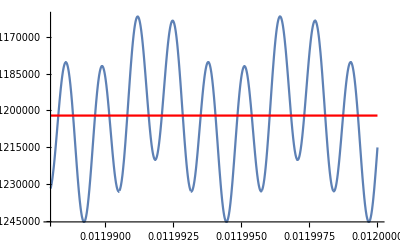

```mathematica
SetDirectory["C:\\Users\\hp\\Desktop\\ICL\\Simulation\\Image and animaiton"];
B = 1.0;
V0 = 30.0;
Va = 6.0;
tEnd  = 12000*10^-6;
isLaseron = 1;
offset = 0;
result = TwoIonAxialisation[B,offset,V0,Va,tEnd,isLaseron];
sol = result[[1]];(* solution of ion trap system *)

θ[t1_]:=ArcTan[y1[t]/x1[t]]/.sol/.t->t1;
ω[t2_]:=D[θ[t1],t1]/.t1->t2;
ωc= (q B)/m;
p1 = Plot[ω[k],{k,0.999*tEnd,tEnd}];
p2 = Plot[-ωc/2,{k,0.999*tEnd,tEnd},PlotStyle->Red];
angularFreq = Show[p1,p2](* ploting equilibrium angular frequency vs ωc/2 *)
motion = result[[3]]
```